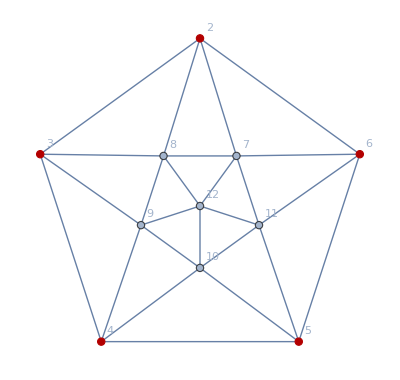

```mathematica
baseg =Graph[VertexDelete[ Graph[plantri[[1]]],1],GraphHighlight->{2,3,4,5,6}, GraphLayout->"TutteEmbedding", VertexLabels->"Name"]
```

```mathematica
EmbedGraph[key_]:=Block[{val=newAssoc[key], sets, reference={2,6,5,4,3}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[10000]]],1];
g=EdgeDelete[ g,{2<->6,6<->5,5<->4,4<->3,3<->2}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
CosyPrint2[47694]
```

-Graphics-   -Graphics-   x47685==x47694+x49972
x40887==x47694+x56770
x47694==x49963+x52232   (2 | 2 | 1 | 0 | 2
2 | 2 | 1 | 0 | 2
1 | 1 | 2 | 1 | 1
0 | 0 | 1 | 2 | 0
2 | 2 | 1 | 0 | 2){47694→d1/12+d10/12+d2/12-d3/12+d4/12-d5/12-d6/12-d7/12+d8/12+d9/12-(5 k1)/12+k10/12+k11/12-(5 k12)/12+k13/12-k14/12+k15/12+k2/12-(5 k3)/12-k4/12+k5/12+k6/12+k7/12+k8/12-k9/12-q1/24-q10/24+(11 q2)/24-q3/24-q4/24-q5/24-q6/24-q7/24-q8/24-q9/24-t1/4-t10/4+(3 t2)/4+t3/12+t4/12+t5/12+t6/12+t7/12-t8/4+t9/12-v1/24-v2/24-v3/24+v4/8-v5/24≥0,}

```mathematica
Table[{key,If[
PlanarGraphQ[EmbedGraph[key]],
newAssoc[key]["comp"]=Greater,
newAssoc[key]["comp"]=GreaterEqual
]},{key,Keys[newAssoc]}]
```

{{0,Greater},{1,Greater},{2,Greater},{3,Greater},{4,Greater},{6,Greater},{9,Greater},{10,Greater},{12,Greater},{13,Greater},{14,Greater},{16,Greater},{18,Greater},{22,Greater},{26,Greater},{27,Greater},{28,Greater},{30,Greater},{31,Greater},{36,Greater},{37,Greater},{39,Greater},{40,Greater},{45,Greater},{49,Greater},{54,Greater},{63,Greater},{72,Greater},{81,Greater},{82,Greater},{84,GreaterEqual},{85,GreaterEqual},{87,GreaterEqual},{90,Greater},{91,Greater},{93,GreaterEqual},{94,GreaterEqual},{97,GreaterEqual},{108,Greater},{109,Greater},{110,Greater},{111,GreaterEqual},{112,GreaterEqual},{117,Greater},{118,Greater},{120,GreaterEqual},{121,GreaterEqual},{122,Greater},{136,Greater},{145,Greater},{162,Greater},{165,GreaterEqual},{168,GreaterEqual},{190,Greater},{193,GreaterEqual},{218,Greater},{243,Greater},{244,Greater},{245,Greater},{246,Greater},{247,Greater},{252,Greater},{253,Greater},{255,Greater},{256,Greater},{257,Greater},{270,Greater},{271,Greater},{273,Greater},{274,Greater},{276,Greater},{279,Greater},{280,Greater},{282,Greater},{283,Greater},{286,Greater},{300,Greater},{309,Greater},{324,Greater},{325,Greater},{327,GreaterEqual},{328,GreaterEqual},{333,Greater},{334,Greater},{336,GreaterEqual},{337,GreaterEqual},{342,Greater},{346,Greater},{351,Greater},{352,Greater},{353,Greater},{354,GreaterEqual},{355,GreaterEqual},{357,GreaterEqual},{360,Greater},{361,Greater},{363,GreaterEqual},{364,GreaterEqual},{365,Greater},{367,GreaterEqual},{369,Greater},{373,Greater},{377,Greater},{382,Greater},{391,Greater},{400,Greater},{414,Greater},{417,GreaterEqual},{442,Greater},{445,GreaterEqual},{448,GreaterEqual},{473,Greater},{486,Greater},{487,Greater},{488,Greater},{516,Greater},{517,Greater},{546,Greater},{576,Greater},{577,Greater},{606,Greater},{607,Greater},{608,Greater},{637,Greater},{666,Greater},{697,Greater},{728,Greater},{729,Greater},{730,Greater},{732,Greater},{733,Greater},{738,Greater},{739,Greater},{741,Greater},{742,Greater},{747,Greater},{751,Greater},{756,Greater},{757,Greater},{759,Greater},{760,Greater},{765,Greater},{766,Greater},{768,Greater},{769,Greater},{774,Greater},{778,Greater},{810,Greater},{811,Greater},{813,GreaterEqual},{814,GreaterEqual},{819,Greater},{820,Greater},{822,GreaterEqual},{823,GreaterEqual},{837,Greater},{838,Greater},{840,GreaterEqual},{841,GreaterEqual},{846,Greater},{847,Greater},{849,GreaterEqual},{850,GreaterEqual},{891,Greater},{894,GreaterEqual},{919,Greater},{922,GreaterEqual},{972,Greater},{973,Greater},{975,Greater},{976,Greater},{981,Greater},{982,Greater},{984,Greater},{985,Greater},{999,Greater},{1000,Greater},{1002,Greater},{1003,Greater},{1008,Greater},{1009,Greater},{1011,Greater},{1012,Greater},{1053,Greater},{1054,Greater},{1056,GreaterEqual},{1057,GreaterEqual},{1062,Greater},{1063,Greater},{1065,GreaterEqual},{1066,GreaterEqual},{1071,Greater},{1075,Greater},{1080,Greater},{1081,Greater},{1083,GreaterEqual},{1084,GreaterEqual},{1089,Greater},{1090,Greater},{1092,GreaterEqual},{1093,GreaterEqual},{1098,Greater},{1102,Greater},{1143,Greater},{1146,GreaterEqual},{1171,Greater},{1174,GreaterEqual},{1215,Greater},{1216,Greater},{1245,Greater},{1246,Greater},{1305,Greater},{1306,Greater},{1335,Greater},{1336,Greater},{1395,Greater},{1426,Greater},{1458,Greater},{1467,Greater},{1476,Greater},{1539,Greater},{1548,Greater},{1620,Greater},{1701,Greater},{1710,Greater},{1782,Greater},{1791,Greater},{1800,Greater},{1872,Greater},{1944,Greater},{2034,Greater},{2124,Greater},{2187,Greater},{2188,Greater},{2190,GreaterEqual},{2191,GreaterEqual},{2193,GreaterEqual},{2196,Greater},{2197,Greater},{2199,GreaterEqual},{2200,GreaterEqual},{2203,GreaterEqual},{2214,GreaterEqual},{2215,GreaterEqual},{2217,GreaterEqual},{2218,GreaterEqual},{2223,GreaterEqual},{2224,GreaterEqual},{2226,GreaterEqual},{2227,GreaterEqual},{2241,GreaterEqual},{2250,GreaterEqual},{2268,Greater},{2269,Greater},{2271,GreaterEqual},{2272,GreaterEqual},{2274,GreaterEqual},{2277,Greater},{2278,Greater},{2280,GreaterEqual},{2281,GreaterEqual},{2284,GreaterEqual},{2295,GreaterEqual},{2296,GreaterEqual},{2298,GreaterEqual},{2299,GreaterEqual},{2304,GreaterEqual},{2305,GreaterEqual},{2307,GreaterEqual},{2308,GreaterEqual},{2323,GreaterEqual},{2332,GreaterEqual},{2430,Greater},{2431,Greater},{2433,GreaterEqual},{2434,GreaterEqual},{2439,Greater},{2440,Greater},{2442,GreaterEqual},{2443,GreaterEqual},{2457,GreaterEqual},{2458,GreaterEqual},{2460,GreaterEqual},{2461,GreaterEqual},{2463,GreaterEqual},{2466,GreaterEqual},{2467,GreaterEqual},{2469,GreaterEqual},{2470,GreaterEqual},{2473,GreaterEqual},{2487,GreaterEqual},{2496,GreaterEqual},{2511,Greater},{2512,Greater},{2514,GreaterEqual},{2515,GreaterEqual},{2520,Greater},{2521,Greater},{2523,GreaterEqual},{2524,GreaterEqual},{2538,GreaterEqual},{2539,GreaterEqual},{2541,GreaterEqual},{2542,GreaterEqual},{2544,GreaterEqual},{2547,GreaterEqual},{2548,GreaterEqual},{2550,GreaterEqual},{2551,GreaterEqual},{2554,GreaterEqual},{2569,GreaterEqual},{2578,GreaterEqual},{2673,Greater},{2674,Greater},{2703,GreaterEqual},{2704,GreaterEqual},{2733,GreaterEqual},{2763,Greater},{2764,Greater},{2793,GreaterEqual},{2794,GreaterEqual},{2824,GreaterEqual},{2916,Greater},{2917,Greater},{2918,Greater},{2919,GreaterEqual},{2920,GreaterEqual},{2925,Greater},{2926,Greater},{2928,GreaterEqual},{2929,GreaterEqual},{2930,Greater},{2943,GreaterEqual},{2944,GreaterEqual},{2946,GreaterEqual},{2947,GreaterEqual},{2952,GreaterEqual},{2953,GreaterEqual},{2955,GreaterEqual},{2956,GreaterEqual},{2997,Greater},{2998,Greater},{3000,GreaterEqual},{3001,GreaterEqual},{3006,Greater},{3007,Greater},{3009,GreaterEqual},{3010,GreaterEqual},{3024,GreaterEqual},{3025,GreaterEqual},{3026,Greater},{3027,GreaterEqual},{3028,GreaterEqual},{3033,GreaterEqual},{3034,GreaterEqual},{3036,GreaterEqual},{3037,GreaterEqual},{3038,Greater},{3159,Greater},{3160,Greater},{3161,Greater},{3162,GreaterEqual},{3163,GreaterEqual},{3168,Greater},{3169,Greater},{3171,GreaterEqual},{3172,GreaterEqual},{3173,Greater},{3186,GreaterEqual},{3187,GreaterEqual},{3189,GreaterEqual},{3190,GreaterEqual},{3195,GreaterEqual},{3196,GreaterEqual},{3198,GreaterEqual},{3199,GreaterEqual},{3240,Greater},{3241,Greater},{3243,GreaterEqual},{3244,GreaterEqual},{3249,Greater},{3250,Greater},{3252,GreaterEqual},{3253,GreaterEqual},{3267,GreaterEqual},{3268,GreaterEqual},{3269,Greater},{3270,GreaterEqual},{3271,GreaterEqual},{3276,GreaterEqual},{3277,GreaterEqual},{3279,GreaterEqual},{3280,GreaterEqual},{3281,Greater},{3402,Greater},{3403,Greater},{3404,Greater},{3432,GreaterEqual},{3433,GreaterEqual},{3492,Greater},{3493,Greater},{3522,GreaterEqual},{3523,GreaterEqual},{3524,Greater},{3646,Greater},{3655,Greater},{3727,Greater},{3736,Greater},{3889,Greater},{3898,Greater},{3970,Greater},{3979,Greater},{4132,Greater},{4222,Greater},{4374,Greater},{4377,GreaterEqual},{4380,GreaterEqual},{4401,GreaterEqual},{4404,GreaterEqual},{4428,GreaterEqual},{4617,Greater},{4620,GreaterEqual},{4644,GreaterEqual},{4647,GreaterEqual},{4650,GreaterEqual},{4674,GreaterEqual},{4860,Greater},{4890,GreaterEqual},{4920,GreaterEqual},{5104,Greater},{5107,GreaterEqual},{5131,GreaterEqual},{5134,GreaterEqual},{5347,Greater},{5350,GreaterEqual},{5374,GreaterEqual},{5377,GreaterEqual},{5590,Greater},{5620,GreaterEqual},{5834,Greater},{6077,Greater},{6320,Greater},{6561,Greater},{6562,Greater},{6563,Greater},{6564,Greater},{6565,Greater},{6570,Greater},{6571,Greater},{6573,Greater},{6574,Greater},{6575,Greater},{6588,GreaterEqual},{6589,GreaterEqual},{6591,GreaterEqual},{6592,GreaterEqual},{6597,GreaterEqual},{6598,GreaterEqual},{6600,GreaterEqual},{6601,GreaterEqual},{6615,GreaterEqual},{6624,GreaterEqual},{6642,GreaterEqual},{6643,GreaterEqual},{6645,GreaterEqual},{6646,GreaterEqual},{6651,GreaterEqual},{6652,GreaterEqual},{6654,GreaterEqual},{6655,GreaterEqual},{6669,GreaterEqual},{6670,GreaterEqual},{6671,GreaterEqual},{6672,GreaterEqual},{6673,GreaterEqual},{6678,GreaterEqual},{6679,GreaterEqual},{6681,GreaterEqual},{6682,GreaterEqual},{6683,GreaterEqual},{6697,GreaterEqual},{6706,GreaterEqual},{6723,GreaterEqual},{6726,GreaterEqual},{6751,GreaterEqual},{6754,GreaterEqual},{6779,GreaterEqual},{6804,Greater},{6805,Greater},{6806,Greater},{6807,Greater},{6808,Greater},{6813,Greater},{6814,Greater},{6816,Greater},{6817,Greater},{6818,Greater},{6831,GreaterEqual},{6832,GreaterEqual},{6834,GreaterEqual},{6835,GreaterEqual},{6840,GreaterEqual},{6841,GreaterEqual},{6843,GreaterEqual},{6844,GreaterEqual},{6861,GreaterEqual},{6870,GreaterEqual},{6885,GreaterEqual},{6886,GreaterEqual},{6888,GreaterEqual},{6889,GreaterEqual},{6894,GreaterEqual},{6895,GreaterEqual},{6897,GreaterEqual},{6898,GreaterEqual},{6912,GreaterEqual},{6913,GreaterEqual},{6914,GreaterEqual},{6915,GreaterEqual},{6916,GreaterEqual},{6921,GreaterEqual},{6922,GreaterEqual},{6924,GreaterEqual},{6925,GreaterEqual},{6926,GreaterEqual},{6943,GreaterEqual},{6952,GreaterEqual},{6975,GreaterEqual},{6978,GreaterEqual},{7003,GreaterEqual},{7006,GreaterEqual},{7034,GreaterEqual},{7290,Greater},{7291,Greater},{7293,Greater},{7294,Greater},{7296,Greater},{7299,Greater},{7300,Greater},{7302,Greater},{7303,Greater},{7306,Greater},{7317,GreaterEqual},{7318,GreaterEqual},{7320,GreaterEqual},{7321,GreaterEqual},{7326,GreaterEqual},{7327,GreaterEqual},{7329,GreaterEqual},{7330,GreaterEqual},{7371,GreaterEqual},{7372,GreaterEqual},{7374,GreaterEqual},{7375,GreaterEqual},{7377,GreaterEqual},{7380,GreaterEqual},{7381,GreaterEqual},{7383,GreaterEqual},{7384,GreaterEqual},{7387,GreaterEqual},{7398,GreaterEqual},{7399,GreaterEqual},{7401,GreaterEqual},{7402,GreaterEqual},{7407,GreaterEqual},{7408,GreaterEqual},{7410,GreaterEqual},{7411,GreaterEqual},{7452,GreaterEqual},{7455,GreaterEqual},{7458,GreaterEqual},{7480,GreaterEqual},{7483,GreaterEqual},{7533,Greater},{7534,Greater},{7536,Greater},{7537,Greater},{7542,Greater},{7543,Greater},{7545,Greater},{7546,Greater},{7560,GreaterEqual},{7561,GreaterEqual},{7563,GreaterEqual},{7564,GreaterEqual},{7566,Greater},{7569,GreaterEqual},{7570,GreaterEqual},{7572,GreaterEqual},{7573,GreaterEqual},{7576,Greater},{7614,GreaterEqual},{7615,GreaterEqual},{7617,GreaterEqual},{7618,GreaterEqual},{7623,GreaterEqual},{7624,GreaterEqual},{7626,GreaterEqual},{7627,GreaterEqual},{7641,GreaterEqual},{7642,GreaterEqual},{7644,GreaterEqual},{7645,GreaterEqual},{7647,GreaterEqual},{7650,GreaterEqual},{7651,GreaterEqual},{7653,GreaterEqual},{7654,GreaterEqual},{7657,GreaterEqual},{7704,GreaterEqual},{7707,GreaterEqual},{7732,GreaterEqual},{7735,GreaterEqual},{7738,GreaterEqual},{8022,Greater},{8031,Greater},{8103,GreaterEqual},{8112,GreaterEqual},{8184,GreaterEqual},{8265,Greater},{8274,Greater},{8346,GreaterEqual},{8355,GreaterEqual},{8436,GreaterEqual},{8748,Greater},{8749,Greater},{8751,GreaterEqual},{8752,GreaterEqual},{8757,Greater},{8758,Greater},{8760,GreaterEqual},{8761,GreaterEqual},{8766,Greater},{8770,Greater},{8775,GreaterEqual},{8776,GreaterEqual},{8778,GreaterEqual},{8779,GreaterEqual},{8784,GreaterEqual},{8785,GreaterEqual},{8787,GreaterEqual},{8788,GreaterEqual},{8793,GreaterEqual},{8797,GreaterEqual},{8802,GreaterEqual},{8811,GreaterEqual},{8820,GreaterEqual},{8829,GreaterEqual},{8830,GreaterEqual},{8832,GreaterEqual},{8833,GreaterEqual},{8838,GreaterEqual},{8839,GreaterEqual},{8841,GreaterEqual},{8842,GreaterEqual},{8856,GreaterEqual},{8857,GreaterEqual},{8859,GreaterEqual},{8860,GreaterEqual},{8865,GreaterEqual},{8866,GreaterEqual},{8868,GreaterEqual},{8869,GreaterEqual},{8884,GreaterEqual},{8893,GreaterEqual},{8991,Greater},{8992,Greater},{8994,GreaterEqual},{8995,GreaterEqual},{9000,Greater},{9001,Greater},{9003,GreaterEqual},{9004,GreaterEqual},{9018,GreaterEqual},{9019,GreaterEqual},{9021,GreaterEqual},{9022,GreaterEqual},{9027,GreaterEqual},{9028,GreaterEqual},{9030,GreaterEqual},{9031,GreaterEqual},{9048,GreaterEqual},{9057,GreaterEqual},{9072,GreaterEqual},{9073,GreaterEqual},{9075,GreaterEqual},{9076,GreaterEqual},{9081,GreaterEqual},{9082,GreaterEqual},{9084,GreaterEqual},{9085,GreaterEqual},{9090,Greater},{9094,Greater},{9099,GreaterEqual},{9100,GreaterEqual},{9102,GreaterEqual},{9103,GreaterEqual},{9108,GreaterEqual},{9109,GreaterEqual},{9111,GreaterEqual},{9112,GreaterEqual},{9117,GreaterEqual},{9121,GreaterEqual},{9130,GreaterEqual},{9139,GreaterEqual},{9148,GreaterEqual},{9477,Greater},{9478,Greater},{9479,Greater},{9480,GreaterEqual},{9481,GreaterEqual},{9483,GreaterEqual},{9486,Greater},{9487,Greater},{9489,GreaterEqual},{9490,GreaterEqual},{9491,Greater},{9493,GreaterEqual},{9495,Greater},{9499,Greater},{9503,Greater},{9504,GreaterEqual},{9505,GreaterEqual},{9507,GreaterEqual},{9508,GreaterEqual},{9513,GreaterEqual},{9514,GreaterEqual},{9516,GreaterEqual},{9517,GreaterEqual},{9522,GreaterEqual},{9526,GreaterEqual},{9558,GreaterEqual},{9559,GreaterEqual},{9561,GreaterEqual},{9562,GreaterEqual},{9564,GreaterEqual},{9567,GreaterEqual},{9568,GreaterEqual},{9570,GreaterEqual},{9571,GreaterEqual},{9574,GreaterEqual},{9585,GreaterEqual},{9586,GreaterEqual},{9587,GreaterEqual},{9588,GreaterEqual},{9589,GreaterEqual},{9594,GreaterEqual},{9595,GreaterEqual},{9597,GreaterEqual},{9598,GreaterEqual},{9599,GreaterEqual},{9720,Greater},{9721,Greater},{9722,Greater},{9723,GreaterEqual},{9724,GreaterEqual},{9729,Greater},{9730,Greater},{9732,GreaterEqual},{9733,GreaterEqual},{9734,Greater},{9747,GreaterEqual},{9748,GreaterEqual},{9750,GreaterEqual},{9751,GreaterEqual},{9753,GreaterEqual},{9756,GreaterEqual},{9757,GreaterEqual},{9759,GreaterEqual},{9760,GreaterEqual},{9763,GreaterEqual},{9801,GreaterEqual},{9802,GreaterEqual},{9804,GreaterEqual},{9805,GreaterEqual},{9810,GreaterEqual},{9811,GreaterEqual},{9813,GreaterEqual},{9814,GreaterEqual},{9819,Greater},{9823,Greater},{9828,GreaterEqual},{9829,GreaterEqual},{9830,GreaterEqual},{9831,GreaterEqual},{9832,GreaterEqual},{9834,GreaterEqual},{9837,GreaterEqual},{9838,GreaterEqual},{9840,GreaterEqual},{9841,GreaterEqual},{9842,GreaterEqual},{9844,GreaterEqual},{9846,GreaterEqual},{9850,GreaterEqual},{9854,Greater},{10210,Greater},{10219,Greater},{10228,Greater},{10291,GreaterEqual},{10300,GreaterEqual},{10453,Greater},{10462,Greater},{10534,GreaterEqual},{10543,GreaterEqual},{10552,Greater},{10944,Greater},{10947,GreaterEqual},{10971,GreaterEqual},{10974,GreaterEqual},{10998,GreaterEqual},{11187,Greater},{11190,GreaterEqual},{11214,GreaterEqual},{11217,GreaterEqual},{11244,GreaterEqual},{11674,Greater},{11677,GreaterEqual},{11680,GreaterEqual},{11701,GreaterEqual},{11704,GreaterEqual},{11917,Greater},{11920,GreaterEqual},{11944,GreaterEqual},{11947,GreaterEqual},{11950,GreaterEqual},{12407,Greater},{12650,Greater},{13122,Greater},{13123,Greater},{13124,Greater},{13149,GreaterEqual},{13150,GreaterEqual},{13176,GreaterEqual},{13203,GreaterEqual},{13204,GreaterEqual},{13230,GreaterEqual},{13231,GreaterEqual},{13232,GreaterEqual},{13258,GreaterEqual},{13284,GreaterEqual},{13312,GreaterEqual},{13340,GreaterEqual},{13854,Greater},{13855,Greater},{13881,GreaterEqual},{13882,GreaterEqual},{13935,GreaterEqual},{13936,GreaterEqual},{13962,GreaterEqual},{13963,GreaterEqual},{14016,GreaterEqual},{14044,GreaterEqual},{14586,Greater},{14667,GreaterEqual},{14748,GreaterEqual},{15318,Greater},{15319,Greater},{15345,GreaterEqual},{15346,GreaterEqual},{15372,GreaterEqual},{15399,GreaterEqual},{15400,GreaterEqual},{15426,GreaterEqual},{15427,GreaterEqual},{15454,GreaterEqual},{16050,Greater},{16051,Greater},{16052,Greater},{16077,GreaterEqual},{16078,GreaterEqual},{16131,GreaterEqual},{16132,GreaterEqual},{16158,GreaterEqual},{16159,GreaterEqual},{16160,GreaterEqual},{16783,Greater},{16864,GreaterEqual},{17514,Greater},{17541,GreaterEqual},{17568,GreaterEqual},{18247,Greater},{18274,GreaterEqual},{18980,Greater},{19683,Greater},{19684,Greater},{19685,Greater},{19686,Greater},{19687,Greater},{19689,Greater},{19692,Greater},{19693,Greater},{19695,Greater},{19696,Greater},{19697,Greater},{19699,Greater},{19701,Greater},{19705,Greater},{19709,Greater},{19710,Greater},{19711,Greater},{19713,Greater},{19714,Greater},{19719,Greater},{19720,Greater},{19722,Greater},{19723,Greater},{19728,Greater},{19732,Greater},{19764,Greater},{19765,Greater},{19767,GreaterEqual},{19768,GreaterEqual},{19770,GreaterEqual},{19773,Greater},{19774,Greater},{19776,GreaterEqual},{19777,GreaterEqual},{19780,GreaterEqual},{19791,Greater},{19792,Greater},{19793,Greater},{19794,GreaterEqual},{19795,GreaterEqual},{19800,Greater},{19801,Greater},{19803,GreaterEqual},{19804,GreaterEqual},{19805,Greater},{19926,Greater},{19927,Greater},{19928,Greater},{19929,Greater},{19930,Greater},{19935,Greater},{19936,Greater},{19938,Greater},{19939,Greater},{19940,Greater},{19953,Greater},{19954,Greater},{19956,Greater},{19957,Greater},{19959,Greater},{19962,Greater},{19963,Greater},{19965,Greater},{19966,Greater},{19969,Greater},{20007,Greater},{20008,Greater},{20010,GreaterEqual},{20011,GreaterEqual},{20016,Greater},{20017,Greater},{20019,GreaterEqual},{20020,GreaterEqual},{20025,Greater},{20029,Greater},{20034,Greater},{20035,Greater},{20036,Greater},{20037,GreaterEqual},{20038,GreaterEqual},{20040,GreaterEqual},{20043,Greater},{20044,Greater},{20046,GreaterEqual},{20047,GreaterEqual},{20048,Greater},{20050,GreaterEqual},{20052,Greater},{20056,Greater},{20060,Greater},{20412,Greater},{20413,Greater},{20415,Greater},{20416,Greater},{20421,Greater},{20422,Greater},{20424,Greater},{20425,Greater},{20430,Greater},{20434,Greater},{20439,Greater},{20440,Greater},{20442,Greater},{20443,Greater},{20448,Greater},{20449,Greater},{20451,Greater},{20452,Greater},{20457,Greater},{20461,Greater},{20466,Greater},{20475,Greater},{20484,Greater},{20493,Greater},{20494,Greater},{20496,GreaterEqual},{20497,GreaterEqual},{20502,Greater},{20503,Greater},{20505,GreaterEqual},{20506,GreaterEqual},{20520,Greater},{20521,Greater},{20523,GreaterEqual},{20524,GreaterEqual},{20529,Greater},{20530,Greater},{20532,GreaterEqual},{20533,GreaterEqual},{20548,Greater},{20557,Greater},{20655,Greater},{20656,Greater},{20658,Greater},{20659,Greater},{20664,Greater},{20665,Greater},{20667,Greater},{20668,Greater},{20682,Greater},{20683,Greater},{20685,Greater},{20686,Greater},{20691,Greater},{20692,Greater},{20694,Greater},{20695,Greater},{20712,Greater},{20721,Greater},{20736,Greater},{20737,Greater},{20739,GreaterEqual},{20740,GreaterEqual},{20745,Greater},{20746,Greater},{20748,GreaterEqual},{20749,GreaterEqual},{20754,Greater},{20758,Greater},{20763,Greater},{20764,Greater},{20766,GreaterEqual},{20767,GreaterEqual},{20772,Greater},{20773,Greater},{20775,GreaterEqual},{20776,GreaterEqual},{20781,Greater},{20785,Greater},{20794,Greater},{20803,Greater},{20812,Greater},{21168,Greater},{21177,Greater},{21186,Greater},{21249,Greater},{21258,Greater},{21411,Greater},{21420,Greater},{21492,Greater},{21501,Greater},{21510,Greater},{21870,Greater},{21871,Greater},{21873,GreaterEqual},{21874,GreaterEqual},{21876,GreaterEqual},{21879,Greater},{21880,Greater},{21882,GreaterEqual},{21883,GreaterEqual},{21886,GreaterEqual},{21897,GreaterEqual},{21898,GreaterEqual},{21900,GreaterEqual},{21901,GreaterEqual},{21906,GreaterEqual},{21907,GreaterEqual},{21909,GreaterEqual},{21910,GreaterEqual},{21951,Greater},{21952,Greater},{21954,GreaterEqual},{21955,GreaterEqual},{21957,GreaterEqual},{21960,Greater},{21961,Greater},{21963,GreaterEqual},{21964,GreaterEqual},{21967,GreaterEqual},{21978,GreaterEqual},{21979,GreaterEqual},{21981,GreaterEqual},{21982,GreaterEqual},{21987,GreaterEqual},{21988,GreaterEqual},{21990,GreaterEqual},{21991,GreaterEqual},{22032,Greater},{22035,GreaterEqual},{22038,GreaterEqual},{22060,Greater},{22063,GreaterEqual},{22113,Greater},{22114,Greater},{22116,GreaterEqual},{22117,GreaterEqual},{22122,Greater},{22123,Greater},{22125,GreaterEqual},{22126,GreaterEqual},{22140,GreaterEqual},{22141,GreaterEqual},{22143,GreaterEqual},{22144,GreaterEqual},{22146,GreaterEqual},{22149,GreaterEqual},{22150,GreaterEqual},{22152,GreaterEqual},{22153,GreaterEqual},{22156,GreaterEqual},{22194,Greater},{22195,Greater},{22197,GreaterEqual},{22198,GreaterEqual},{22203,Greater},{22204,Greater},{22206,GreaterEqual},{22207,GreaterEqual},{22221,GreaterEqual},{22222,GreaterEqual},{22224,GreaterEqual},{22225,GreaterEqual},{22227,GreaterEqual},{22230,GreaterEqual},{22231,GreaterEqual},{22233,GreaterEqual},{22234,GreaterEqual},{22237,GreaterEqual},{22284,Greater},{22287,GreaterEqual},{22312,Greater},{22315,GreaterEqual},{22318,GreaterEqual},{22599,Greater},{22600,Greater},{22601,Greater},{22602,GreaterEqual},{22603,GreaterEqual},{22608,Greater},{22609,Greater},{22611,GreaterEqual},{22612,GreaterEqual},{22613,Greater},{22626,GreaterEqual},{22627,GreaterEqual},{22629,GreaterEqual},{22630,GreaterEqual},{22635,GreaterEqual},{22636,GreaterEqual},{22638,GreaterEqual},{22639,GreaterEqual},{22653,GreaterEqual},{22662,GreaterEqual},{22680,Greater},{22681,Greater},{22683,GreaterEqual},{22684,GreaterEqual},{22689,Greater},{22690,Greater},{22692,GreaterEqual},{22693,GreaterEqual},{22707,GreaterEqual},{22708,GreaterEqual},{22709,Greater},{22710,GreaterEqual},{22711,GreaterEqual},{22716,GreaterEqual},{22717,GreaterEqual},{22719,GreaterEqual},{22720,GreaterEqual},{22721,Greater},{22735,GreaterEqual},{22744,GreaterEqual},{22761,Greater},{22764,GreaterEqual},{22789,Greater},{22792,GreaterEqual},{22817,Greater},{22842,Greater},{22843,Greater},{22844,Greater},{22845,GreaterEqual},{22846,GreaterEqual},{22851,Greater},{22852,Greater},{22854,GreaterEqual},{22855,GreaterEqual},{22856,Greater},{22869,GreaterEqual},{22870,GreaterEqual},{22872,GreaterEqual},{22873,GreaterEqual},{22878,GreaterEqual},{22879,GreaterEqual},{22881,GreaterEqual},{22882,GreaterEqual},{22899,GreaterEqual},{22908,GreaterEqual},{22923,Greater},{22924,Greater},{22926,GreaterEqual},{22927,GreaterEqual},{22932,Greater},{22933,Greater},{22935,GreaterEqual},{22936,GreaterEqual},{22950,GreaterEqual},{22951,GreaterEqual},{22952,Greater},{22953,GreaterEqual},{22954,GreaterEqual},{22959,GreaterEqual},{22960,GreaterEqual},{22962,GreaterEqual},{22963,GreaterEqual},{22964,Greater},{22981,GreaterEqual},{22990,GreaterEqual},{23013,Greater},{23016,GreaterEqual},{23041,Greater},{23044,GreaterEqual},{23072,Greater},{23356,Greater},{23365,Greater},{23437,Greater},{23446,Greater},{23518,Greater},{23599,Greater},{23608,Greater},{23680,Greater},{23689,Greater},{23770,Greater},{24138,Greater},{24141,GreaterEqual},{24144,GreaterEqual},{24165,GreaterEqual},{24168,GreaterEqual},{24381,Greater},{24384,GreaterEqual},{24408,GreaterEqual},{24411,GreaterEqual},{24414,GreaterEqual},{24868,Greater},{24871,GreaterEqual},{24895,GreaterEqual},{24898,GreaterEqual},{24922,GreaterEqual},{25111,Greater},{25114,GreaterEqual},{25138,GreaterEqual},{25141,GreaterEqual},{25168,GreaterEqual},{25625,Greater},{25868,Greater},{26244,Greater},{26245,Greater},{26246,Greater},{26247,Greater},{26248,Greater},{26253,Greater},{26254,Greater},{26256,Greater},{26257,Greater},{26258,Greater},{26271,GreaterEqual},{26272,GreaterEqual},{26274,GreaterEqual},{26275,GreaterEqual},{26280,GreaterEqual},{26281,GreaterEqual},{26283,GreaterEqual},{26284,GreaterEqual},{26325,GreaterEqual},{26326,GreaterEqual},{26328,GreaterEqual},{26329,GreaterEqual},{26334,GreaterEqual},{26335,GreaterEqual},{26337,GreaterEqual},{26338,GreaterEqual},{26352,GreaterEqual},{26353,GreaterEqual},{26354,GreaterEqual},{26355,GreaterEqual},{26356,GreaterEqual},{26361,GreaterEqual},{26362,GreaterEqual},{26364,GreaterEqual},{26365,GreaterEqual},{26366,GreaterEqual},{26487,Greater},{26488,Greater},{26489,Greater},{26490,Greater},{26491,Greater},{26496,Greater},{26497,Greater},{26499,Greater},{26500,Greater},{26501,Greater},{26514,GreaterEqual},{26515,GreaterEqual},{26517,GreaterEqual},{26518,GreaterEqual},{26523,GreaterEqual},{26524,GreaterEqual},{26526,GreaterEqual},{26527,GreaterEqual},{26568,GreaterEqual},{26569,GreaterEqual},{26571,GreaterEqual},{26572,GreaterEqual},{26577,GreaterEqual},{26578,GreaterEqual},{26580,GreaterEqual},{26581,GreaterEqual},{26595,GreaterEqual},{26596,GreaterEqual},{26597,GreaterEqual},{26598,GreaterEqual},{26599,GreaterEqual},{26604,GreaterEqual},{26605,GreaterEqual},{26607,GreaterEqual},{26608,GreaterEqual},{26609,GreaterEqual},{26730,Greater},{26731,Greater},{26732,Greater},{26760,Greater},{26761,Greater},{26820,Greater},{26821,Greater},{26850,Greater},{26851,Greater},{26852,Greater},{26973,Greater},{26974,Greater},{26976,Greater},{26977,Greater},{26979,Greater},{26982,Greater},{26983,Greater},{26985,Greater},{26986,Greater},{26989,Greater},{27000,GreaterEqual},{27001,GreaterEqual},{27003,GreaterEqual},{27004,GreaterEqual},{27009,GreaterEqual},{27010,GreaterEqual},{27012,GreaterEqual},{27013,GreaterEqual},{27027,GreaterEqual},{27036,GreaterEqual},{27054,GreaterEqual},{27055,GreaterEqual},{27057,GreaterEqual},{27058,GreaterEqual},{27060,GreaterEqual},{27063,GreaterEqual},{27064,GreaterEqual},{27066,GreaterEqual},{27067,GreaterEqual},{27070,GreaterEqual},{27081,GreaterEqual},{27082,GreaterEqual},{27084,GreaterEqual},{27085,GreaterEqual},{27090,GreaterEqual},{27091,GreaterEqual},{27093,GreaterEqual},{27094,GreaterEqual},{27109,GreaterEqual},{27118,GreaterEqual},{27216,Greater},{27217,Greater},{27219,Greater},{27220,Greater},{27225,Greater},{27226,Greater},{27228,Greater},{27229,Greater},{27243,GreaterEqual},{27244,GreaterEqual},{27246,GreaterEqual},{27247,GreaterEqual},{27249,Greater},{27252,GreaterEqual},{27253,GreaterEqual},{27255,GreaterEqual},{27256,GreaterEqual},{27259,Greater},{27273,GreaterEqual},{27282,GreaterEqual},{27297,GreaterEqual},{27298,GreaterEqual},{27300,GreaterEqual},{27301,GreaterEqual},{27306,GreaterEqual},{27307,GreaterEqual},{27309,GreaterEqual},{27310,GreaterEqual},{27324,GreaterEqual},{27325,GreaterEqual},{27327,GreaterEqual},{27328,GreaterEqual},{27330,GreaterEqual},{27333,GreaterEqual},{27334,GreaterEqual},{27336,GreaterEqual},{27337,GreaterEqual},{27340,GreaterEqual},{27355,GreaterEqual},{27364,GreaterEqual},{27459,Greater},{27460,Greater},{27489,Greater},{27490,Greater},{27519,Greater},{27549,Greater},{27550,Greater},{27579,Greater},{27580,Greater},{27610,Greater},{27732,Greater},{27741,Greater},{27813,GreaterEqual},{27822,GreaterEqual},{27975,Greater},{27984,Greater},{28056,GreaterEqual},{28065,GreaterEqual},{28218,Greater},{28308,Greater},{28431,Greater},{28432,Greater},{28434,GreaterEqual},{28435,GreaterEqual},{28440,Greater},{28441,Greater},{28443,GreaterEqual},{28444,GreaterEqual},{28449,Greater},{28453,Greater},{28458,GreaterEqual},{28459,GreaterEqual},{28461,GreaterEqual},{28462,GreaterEqual},{28467,GreaterEqual},{28468,GreaterEqual},{28470,GreaterEqual},{28471,GreaterEqual},{28476,GreaterEqual},{28480,GreaterEqual},{28512,GreaterEqual},{28513,GreaterEqual},{28515,GreaterEqual},{28516,GreaterEqual},{28521,GreaterEqual},{28522,GreaterEqual},{28524,GreaterEqual},{28525,GreaterEqual},{28539,GreaterEqual},{28540,GreaterEqual},{28542,GreaterEqual},{28543,GreaterEqual},{28548,GreaterEqual},{28549,GreaterEqual},{28551,GreaterEqual},{28552,GreaterEqual},{28593,GreaterEqual},{28596,GreaterEqual},{28621,GreaterEqual},{28624,GreaterEqual},{28674,Greater},{28675,Greater},{28677,GreaterEqual},{28678,GreaterEqual},{28683,Greater},{28684,Greater},{28686,GreaterEqual},{28687,GreaterEqual},{28701,GreaterEqual},{28702,GreaterEqual},{28704,GreaterEqual},{28705,GreaterEqual},{28710,GreaterEqual},{28711,GreaterEqual},{28713,GreaterEqual},{28714,GreaterEqual},{28755,GreaterEqual},{28756,GreaterEqual},{28758,GreaterEqual},{28759,GreaterEqual},{28764,GreaterEqual},{28765,GreaterEqual},{28767,GreaterEqual},{28768,GreaterEqual},{28773,Greater},{28777,Greater},{28782,GreaterEqual},{28783,GreaterEqual},{28785,GreaterEqual},{28786,GreaterEqual},{28791,GreaterEqual},{28792,GreaterEqual},{28794,GreaterEqual},{28795,GreaterEqual},{28800,GreaterEqual},{28804,GreaterEqual},{28845,GreaterEqual},{28848,GreaterEqual},{28873,GreaterEqual},{28876,GreaterEqual},{28917,Greater},{28918,Greater},{28947,GreaterEqual},{28948,GreaterEqual},{29007,Greater},{29008,Greater},{29037,GreaterEqual},{29038,GreaterEqual},{29097,Greater},{29128,Greater},{29160,Greater},{29161,Greater},{29162,Greater},{29163,GreaterEqual},{29164,GreaterEqual},{29166,GreaterEqual},{29169,Greater},{29170,Greater},{29172,GreaterEqual},{29173,GreaterEqual},{29174,Greater},{29176,GreaterEqual},{29178,Greater},{29182,Greater},{29186,Greater},{29187,GreaterEqual},{29188,GreaterEqual},{29190,GreaterEqual},{29191,GreaterEqual},{29196,GreaterEqual},{29197,GreaterEqual},{29199,GreaterEqual},{29200,GreaterEqual},{29205,GreaterEqual},{29209,GreaterEqual},{29214,GreaterEqual},{29223,GreaterEqual},{29232,GreaterEqual},{29241,GreaterEqual},{29242,GreaterEqual},{29244,GreaterEqual},{29245,GreaterEqual},{29247,GreaterEqual},{29250,GreaterEqual},{29251,GreaterEqual},{29253,GreaterEqual},{29254,GreaterEqual},{29257,GreaterEqual},{29268,GreaterEqual},{29269,GreaterEqual},{29270,GreaterEqual},{29271,GreaterEqual},{29272,GreaterEqual},{29277,GreaterEqual},{29278,GreaterEqual},{29280,GreaterEqual},{29281,GreaterEqual},{29282,GreaterEqual},{29296,GreaterEqual},{29305,GreaterEqual},{29322,GreaterEqual},{29325,GreaterEqual},{29328,GreaterEqual},{29350,GreaterEqual},{29353,GreaterEqual},{29378,GreaterEqual},{29403,Greater},{29404,Greater},{29405,Greater},{29406,GreaterEqual},{29407,GreaterEqual},{29412,Greater},{29413,Greater},{29415,GreaterEqual},{29416,GreaterEqual},{29417,Greater},{29430,GreaterEqual},{29431,GreaterEqual},{29433,GreaterEqual},{29434,GreaterEqual},{29436,GreaterEqual},{29439,GreaterEqual},{29440,GreaterEqual},{29442,GreaterEqual},{29443,GreaterEqual},{29446,GreaterEqual},{29460,GreaterEqual},{29469,GreaterEqual},{29484,GreaterEqual},{29485,GreaterEqual},{29487,GreaterEqual},{29488,GreaterEqual},{29493,GreaterEqual},{29494,GreaterEqual},{29496,GreaterEqual},{29497,GreaterEqual},{29502,Greater},{29506,Greater},{29511,GreaterEqual},{29512,GreaterEqual},{29513,GreaterEqual},{29514,GreaterEqual},{29515,GreaterEqual},{29517,GreaterEqual},{29520,GreaterEqual},{29521,GreaterEqual},{29523,GreaterEqual},{29524,GreaterEqual},{29525,GreaterEqual},{29527,GreaterEqual},{29529,GreaterEqual},{29533,GreaterEqual},{29537,Greater},{29542,GreaterEqual},{29551,GreaterEqual},{29560,GreaterEqual},{29574,GreaterEqual},{29577,GreaterEqual},{29602,GreaterEqual},{29605,GreaterEqual},{29608,GreaterEqual},{29633,GreaterEqual},{29646,Greater},{29647,Greater},{29648,Greater},{29676,GreaterEqual},{29677,GreaterEqual},{29706,GreaterEqual},{29736,Greater},{29737,Greater},{29766,GreaterEqual},{29767,GreaterEqual},{29768,Greater},{29797,GreaterEqual},{29826,Greater},{29857,Greater},{29888,Greater},{29920,Greater},{29929,Greater},{29938,Greater},{30001,GreaterEqual},{30010,GreaterEqual},{30082,GreaterEqual},{30163,Greater},{30172,Greater},{30244,GreaterEqual},{30253,GreaterEqual},{30262,Greater},{30334,GreaterEqual},{30406,Greater},{30496,Greater},{30586,Greater},{30708,Greater},{30711,GreaterEqual},{30735,GreaterEqual},{30738,GreaterEqual},{30951,Greater},{30954,GreaterEqual},{30978,GreaterEqual},{30981,GreaterEqual},{31194,Greater},{31224,GreaterEqual},{31438,Greater},{31441,GreaterEqual},{31444,GreaterEqual},{31465,GreaterEqual},{31468,GreaterEqual},{31492,GreaterEqual},{31681,Greater},{31684,GreaterEqual},{31708,GreaterEqual},{31711,GreaterEqual},{31714,GreaterEqual},{31738,GreaterEqual},{31924,Greater},{31954,GreaterEqual},{31984,GreaterEqual},{32198,Greater},{32441,Greater},{32684,Greater},{33048,Greater},{33049,Greater},{33050,Greater},{33075,GreaterEqual},{33076,GreaterEqual},{33129,GreaterEqual},{33130,GreaterEqual},{33156,GreaterEqual},{33157,GreaterEqual},{33158,GreaterEqual},{33780,Greater},{33781,Greater},{33807,GreaterEqual},{33808,GreaterEqual},{33834,GreaterEqual},{33861,GreaterEqual},{33862,GreaterEqual},{33888,GreaterEqual},{33889,GreaterEqual},{33916,GreaterEqual},{34539,Greater},{34620,GreaterEqual},{35244,Greater},{35245,Greater},{35271,GreaterEqual},{35272,GreaterEqual},{35325,GreaterEqual},{35326,GreaterEqual},{35352,GreaterEqual},{35353,GreaterEqual},{35406,GreaterEqual},{35434,GreaterEqual},{35976,Greater},{35977,Greater},{35978,Greater},{36003,GreaterEqual},{36004,GreaterEqual},{36030,GreaterEqual},{36057,GreaterEqual},{36058,GreaterEqual},{36084,GreaterEqual},{36085,GreaterEqual},{36086,GreaterEqual},{36112,GreaterEqual},{36138,GreaterEqual},{36166,GreaterEqual},{36194,GreaterEqual},{36736,Greater},{36817,GreaterEqual},{36898,GreaterEqual},{37521,Greater},{37548,GreaterEqual},{38254,Greater},{38281,GreaterEqual},{38308,GreaterEqual},{39014,Greater},{39366,Greater},{39367,Greater},{39368,Greater},{39369,Greater},{39370,Greater},{39372,Greater},{39375,Greater},{39376,Greater},{39378,Greater},{39379,Greater},{39380,Greater},{39382,Greater},{39384,Greater},{39388,Greater},{39392,Greater},{40122,Greater},{40123,Greater},{40125,Greater},{40126,Greater},{40131,Greater},{40132,Greater},{40134,Greater},{40135,Greater},{40140,Greater},{40144,Greater},{40878,Greater},{40887,Greater},{40896,Greater},{41634,Greater},{41635,Greater},{41637,GreaterEqual},{41638,GreaterEqual},{41640,GreaterEqual},{41643,Greater},{41644,Greater},{41646,GreaterEqual},{41647,GreaterEqual},{41650,GreaterEqual},{42390,Greater},{42391,Greater},{42392,Greater},{42393,GreaterEqual},{42394,GreaterEqual},{42399,Greater},{42400,Greater},{42402,GreaterEqual},{42403,GreaterEqual},{42404,Greater},{43147,Greater},{43156,Greater},{43902,Greater},{43905,GreaterEqual},{43908,GreaterEqual},{44659,Greater},{44662,GreaterEqual},{45416,Greater},{46170,Greater},{46171,Greater},{46172,Greater},{46173,Greater},{46174,Greater},{46179,Greater},{46180,Greater},{46182,Greater},{46183,Greater},{46184,Greater},{46926,Greater},{46927,Greater},{46929,Greater},{46930,Greater},{46932,Greater},{46935,Greater},{46936,Greater},{46938,Greater},{46939,Greater},{46942,Greater},{47685,Greater},{47694,Greater},{48438,Greater},{48439,Greater},{48441,GreaterEqual},{48442,GreaterEqual},{48447,Greater},{48448,Greater},{48450,GreaterEqual},{48451,GreaterEqual},{48456,Greater},{48460,Greater},{49194,Greater},{49195,Greater},{49196,Greater},{49197,GreaterEqual},{49198,GreaterEqual},{49200,GreaterEqual},{49203,Greater},{49204,Greater},{49206,GreaterEqual},{49207,GreaterEqual},{49208,Greater},{49210,GreaterEqual},{49212,Greater},{49216,Greater},{49220,Greater},{49954,Greater},{49963,Greater},{49972,Greater},{50715,Greater},{50718,GreaterEqual},{51472,Greater},{51475,GreaterEqual},{51478,GreaterEqual},{52232,Greater},{52974,Greater},{52975,Greater},{52976,Greater},{53733,Greater},{53734,Greater},{54492,Greater},{55251,Greater},{55252,Greater},{56010,Greater},{56011,Greater},{56012,Greater},{56770,Greater},{57528,Greater},{58288,Greater},{59048,Greater}}

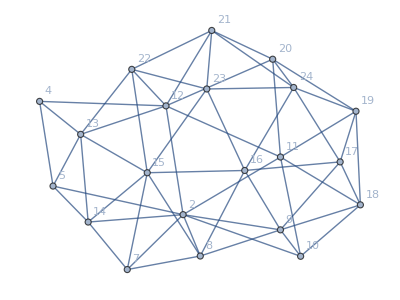

```mathematica
Graph[EmbedGraph[47694],VertexLabels->"Name"]
```

```mathematica
newAssoc[1]
```

<|signature→1,matrix→{{2,0,0,0,0},{0,2,0,0,0},{0,0,2,0,0},{0,0,0,2,1},{0,0,0,1,2}},graph→-Graphics-,vertexsets→{{1},{2},{3},{4},{5}},vertices→{1,2,3,4,5},edges→{{4,5}},relations→{x1==x19684+x39367,x1==x13123+x6562,x1==x2188+x5104,x1==x3646+x730,x1==x244+x487,x1==x190+x82,x1==x136+x28,x1==x10+x22,x1==x16+x4,x1==x0-x2},links→{39367,19684,13123,6562,5104,2188,3646,730,487,244,190,82,136,28,22,10,16,4},colofour→t1,comp→Greater,compwhy→IH|>

```mathematica
Sort[Table[{key,newAssoc[key]["colofour"],ChromaticPolynomial[EmbedGraph[key],4]/24},{key,Select[Keys[newAssoc],MemberQ[myVars,newAssoc[#]["colofour"]]&]}],#1[[3]]>#2[[3]]&]//TableForm
```

0 | z | 3728
3 | t9 | 3000
81 | t10 | 2852
27 | t7 | 2852
6561 | t6 | 2640
2187 | t8 | 2616
1 | t1 | 2520
9 | t2 | 2488
729 | t5 | 2384
19683 | t4 | 2360
243 | t3 | 2348
84 | k7 | 2324
2190 | k6 | 2120
6642 | k8 | 2050
6588 | k9 | 2038
2214 | k10 | 1996
36 | k12 | 1940
19686 | k14 | 1924
810 | k15 | 1848
6562 | k11 | 1772
2430 | k13 | 1682
19692 | k3 | 1598
738 | k1 | 1596
244 | k2 | 1590
19684 | k5 | 1558
972 | k4 | 1500
109 | d1 | 1292
13 | d9 | 1280
273 | d3 | 1268
7293 | d5 | 1112
2917 | d8 | 1112
333 | d10 | 1108
21951 | d4 | 1060
26487 | d6 | 980
20439 | d7 | 980
8757 | d2 | 976
6670 | q6 | 912
2460 | q8 | 894
21954 | q9 | 870
7374 | q10 | 870
19696 | q4 | 796
8784 | q7 | 746
1062 | q5 | 712
3160 | q3 | 702
20448 | q2 | 672
26488 | q1 | 628
364 | v2 | 264
22708 | v5 | 230
9490 | v1 | 224
27246 | v4 | 186
28764 | v3 | 182

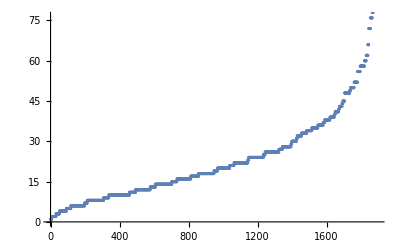

```mathematica
ListPlot[Map[Last,Out[273]]//Sort]
```

```mathematica
CosyPrint2[51478]
```

-Graphics-   -Graphics-   x43908==x51478+x59048   (2 | 2 | 1 | 2 | 1
2 | 2 | 1 | 2 | 1
1 | 1 | 2 | 1 | 2
2 | 2 | 1 | 2 | 1
1 | 1 | 2 | 1 | 2){51478→-d1/12-d10/12-d2/12-d3/12+(5 d4)/12-d5/12-d6/12-d7/12-d8/12-d9/12-k1/12-k10/12-k11/12-k12/12-k13/12+(5 k14)/12-k15/12-k2/12-k3/12-k4/12-k5/12+(5 k6)/12+(5 k7)/12-k8/12-k9/12+q1/24+q10/24+q2/24+q3/24+q4/24+q5/24+q6/24+q7/24+q8/24-(11 q9)/24+t1/4-t10/4+t2/4+t3/4-t4/4+t5/4+t6/4+t7/4-t8/4-(3 t9)/4+v1/24+v2/24+v3/24+v4/24+v5/24≥0,}